# Gaussian wavepacket free evolution

## This notebook uses the analytical solution for free evolution of a gaussian wavepacket. It assumes an initially Heisenberg-limited wavepacket with an initial velocity spread of dv, in units of recoil velocity.

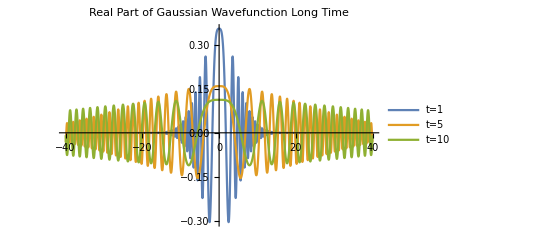

Real part Gaussian wavefunction diffusion long time.png

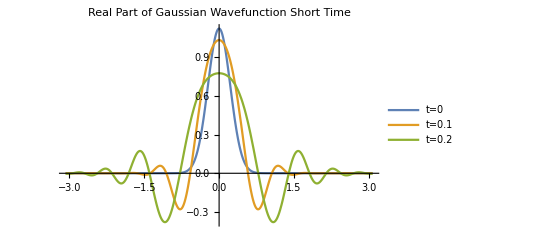

Real part Gaussian wavefunction diffusion short time.png

```mathematica
dv = .05; (*Units of recoil velocity*)

ψ[x_,t_,Δv_] = (Δv/Pi)^(1/4)1/Sqrt[t - ⅈ Δv] Exp[(ⅈ x^2)/(2(t - ⅈ Δv))];
t1=5;
tf = 10;
plotWidth = .2;
apple = Plot[{Re[ψ[x,1,dv]],Re[ψ[x,t1,dv]],Re[ψ[x,tf,dv]]},{x,-tf plotWidth/dv, tf plotWidth/dv}, PlotRange->All, PlotLegends-> {"t=1", "t=5", "t=10"}, PlotLabel->"Real Part of Gaussian Wavefunction Long Time"]
Export["Real part Gaussian wavefunction diffusion long time.png",apple]

banana = Plot[{Re[ψ[x,0,dv]],Re[ψ[x,.1,dv]],Re[ψ[x,.2,dv]]},{x,-tf plotWidth/(13 dv), tf plotWidth/(13 dv)}, PlotRange->All, PlotLegends-> {"t=0", "t=0.1", "t=0.2"}, PlotLabel->"Real Part of Gaussian Wavefunction Short Time"]
Export["Real part Gaussian wavefunction diffusion short time.png",banana]
```